# Calcolo della risposta al gradino unitario per un sistema LTI-TC

```mathematica
ClearAll["Global`*"]
```

Inserisco la terna A, B, C

```mathematica
A={{0,1,0},{0,0,1},{-21,-31,-11}};B={{0},{0},{1}};C1={{1,2,0}};
```

Calcolo la FdT del sistema

```mathematica
G[s_]:=Simplify[C1.Inverse[s IdentityMatrix[3]-A].B]
```

```mathematica
G[s]
```

{{(1+2 s)/(21+31 s+11 s^2+s^3)}}

```mathematica
Solve[Denominator[G[s][[1,1]]]==0,s]
```

{{s→-7},{s→-3},{s→-1}}

```mathematica
Factor[G[s]]
```

{{(1+2 s)/((1+s) (3+s) (7+s))}}

La risposta al Gradino unitario e’ pari a

```mathematica
Factor[G[s][[1,1]]LaplaceTransform[UnitStep[t],t,s]]
```

(1+2 s)/(s (1+s) (3+s) (7+s))

```mathematica
Y[s_]:=G[s][[1,1]]LaplaceTransform[UnitStep[t],t,s]
```

```mathematica
Subscript[C, 1]=lim_(s->0) s Y[s]
```

1/21

```mathematica
Subscript[C, 2]=lim_(s->-3) (s+3) Y[s]
```

-5/24

```mathematica
Subscript[C, 3]=lim_(s->-7) (s+7) Y[s]
```

13/168

```mathematica
Subscript[C, 4]=lim_(s->-1) (s+1) Y[s]
```

1/12

```mathematica
Apart[Y[s]]
```

1/(21 s)+1/(12 (1+s))-5/(24 (3+s))+13/(168 (7+s))

```mathematica
Subscript[y, f][t_]:=Expand[InverseLaplaceTransform[(G[s][[1,1]])/s,s,t]]
```

```mathematica
Subscript[y, f][t]
```

1/21+(13 ⅇ^(-7 t))/168-(5 ⅇ^(-3 t))/24+ⅇ^-t/12

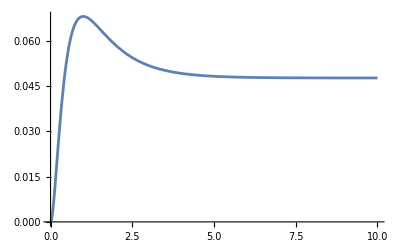

```mathematica
Plot[Subscript[y, f][t],{t,0,10},PlotRange->All]
```

```mathematica
Subscript[y, f][t]
```

1/21+(13 ⅇ^(-7 t))/168-(5 ⅇ^(-3 t))/24+ⅇ^-t/12

```mathematica
Subscript[y, f][t]/.{t->0}
```

0

```mathematica
LaplaceTransform[Sin[t]UnitStep[t],t,s]
```

1/(1+s^2)

Calcolo la risposta forzata al segnale periodico elementare sin(t) 1(t)

```mathematica
Y[s_]:=G[s][[1,1]](1/(s^2+1))
```

```mathematica
Y[s]
```

(1+2 s)/((1+s^2) (21+31 s+11 s^2+s^3))

```mathematica
Factor[Y[s]]
```

(1+2 s)/((1+s) (3+s) (7+s) (1+s^2))

```mathematica
Apart[Y[s]]
```

-1/(24 (1+s))+1/(16 (3+s))-13/(1200 (7+s))+(7-s)/(100 (1+s^2))

Calcolo i coefficienti dell’espansione in fratti semplici

```mathematica
Subscript[D, 1]/(s+ⅈ)+Subscript[D, 2]/(s-ⅈ)+Subscript[D, 3]/(s+1)+Subscript[D, 4]/(s+3)+Subscript[D, 5]/(s+7)
```

-(1/200+(7 ⅈ)/200)/(-ⅈ+s)-(1/200-(7 ⅈ)/200)/(ⅈ+s)-1/(24 (1+s))+1/(16 (3+s))-13/(1200 (7+s))

```mathematica
Subscript[D, 1]=lim_(s->-ⅈ) (s+ⅈ)Y[s]
```

-1/200+(7 ⅈ)/200

```mathematica
Subscript[D, 2]=lim_(s->ⅈ) (s-ⅈ)Y[s]
```

-1/200-(7 ⅈ)/200

```mathematica
Subscript[D, 3]=lim_(s->-1) (s+1)Y[s]
```

-1/24

```mathematica
Subscript[D, 4]=lim_(s->-3) (s+3)Y[s]
```

1/16

```mathematica
Subscript[D, 5]=lim_(s->-7) (s+7)Y[s]
```

-13/1200

```mathematica
Subscript[D, 1]/(s+ⅈ)+Subscript[D, 2]/(s-ⅈ)+Subscript[D, 3]/(s+1)+Subscript[D, 4]/(s+3)+Subscript[D, 5]/(s+7)
```

-(1/200+(7 ⅈ)/200)/(-ⅈ+s)-(1/200-(7 ⅈ)/200)/(ⅈ+s)-1/(24 (1+s))+1/(16 (3+s))-13/(1200 (7+s))

Voglio evidenziare la risposta a regime, la formula e’ questa

```mathematica
ComplexExpand[2 Re[Subscript[D, 2] Exp[I t]]]
```

-Cos[t]/100+(7 Sin[t])/100

Come trasformare la combinazione lineare di due segnali periodici elementari nella forma amplitude-phase

```mathematica
Solve[{(X Sin[t+θ]==-Cos[t]/100+(7 Sin[t])/100)/.{t->0},(D[X Sin[t+θ],t]==D[-Cos[t]/100+(7 Sin[t])/100,t])/.{t->0},X>0},{X,θ}]
```

{{X→ConditionalExpression[1/(10 √2), C[1]∈ℤ],θ→ConditionalExpression[2 ArcTan[(-10+7 √2)/(√2)]+2 π C[1], C[1]∈ℤ]}}